# Examples using the Teukolsky package

This package is still in heavy development. This notebook demonstrates some of the currently implemented features.

Load the packages

```mathematica
<<Teukolsky`
<<KerrGeodesics`
```

Look at the spin-weight s=-2 (gravity) perturbations and the l=m=2 mode. Also set the black hole and orbit parameters and calculate the orbital frequencies using the KerrGeodesics package. Next calculate the eigenvalue λ using the SpinWeightedSpheroidalHarmonics package (automatically loaded by the Teukolsky package). Finally calculate the renormalized angular momentum ν.

```mathematica
s=-2;
l=2;
m=2;

M=1;
a=0.9;
r0=6.;
{Ωr,Ωθ,Ωϕ,Γ}=KerrGeoFreqs[a,r0,0,0];
ω=m Ωϕ;
γ=a ω;
q=a/M;
ϵ=2M ω;

λ=SpinWeightedSpheroidalEigenvalue[s,l,m,γ];
ν=N[RenormalizedAngularMomentum[s,l,m,SetPrecision[q,100],SetPrecision[ϵ,100],SetPrecision[λ,100],Method->"Monodromy"]];
```

## Compute the radial solutions using the MST method

```mathematica
MSTRadialUp[s,l,m,q,ϵ,ν,λ][r0]//Timing
```

{0.051481,-0.962775-1.57419 ⅈ}

```mathematica
MSTRadialIn[s,l,m,q,ϵ,ν,λ][r0]//Timing
```

{0.027871,1006.07+245.996 ⅈ}

```mathematica
MSTRadialUp[s,l,m,q,ϵ,ν,λ]'[r0]//Timing
```

{0.050876,-0.0181017+0.559976 ⅈ}

```mathematica
MSTRadialIn[s,l,m,q,ϵ,ν,λ]'[r0]//Timing
```

{0.043388,757.71+345.67 ⅈ}

```mathematica
MSTRadialIn[s,l,m,q,ϵ,ν,λ]''[r0]//Timing
```

{0.072645,384.924+322.122 ⅈ}

```mathematica
MSTRadialUp[s,l,m,q,ϵ,ν,λ]''[r0]//Timing
```

{0.090482,0.121716-0.105189 ⅈ}

```mathematica
MSTRadialIn[s,l,m,q,ϵ,ν,λ]''''''''''[r0]//Timing
```

{0.632802,0.00218078-0.0122917 ⅈ}

```mathematica
MSTRadialUp[s,l,m,q,ϵ,ν,λ]''''''''''[r0]//Timing
```

{0.675481,1.49105+0.0792649 ⅈ}

## Compute the radial solution via numerical integration of the Sasaki-Nakamura equation

```mathematica
SN=SasakiNakamuraRadialUp[λ,m,a,ω,r0];
```

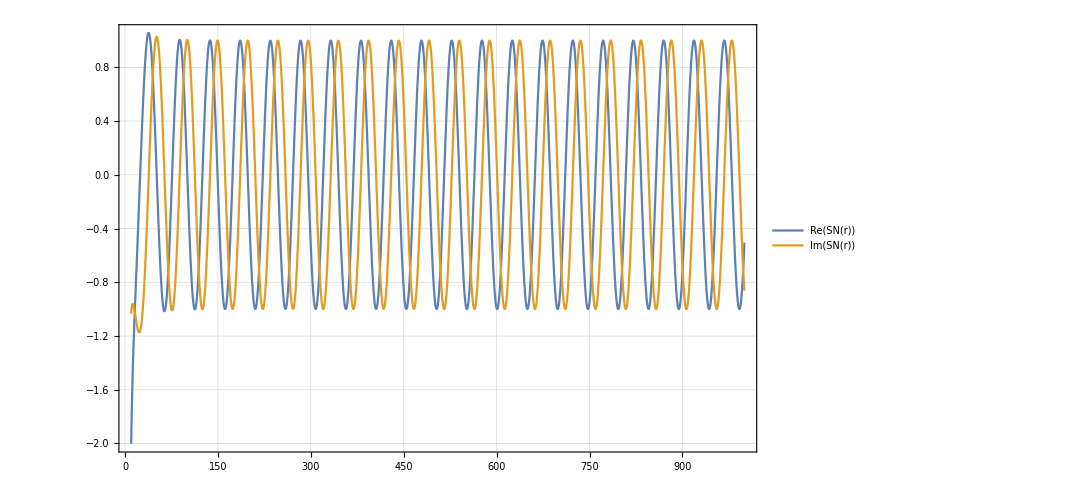

```mathematica
Plot[{SN[r]//Re,SN[r]//Im},{r,1000,10},PlotTheme->"Detailed",ImageSize->800]
```

Compute the Teukolsky Radial solution R_up. Internally this computes the Sasaki-Nakamura solution and then transforms to the Teukolsky solution

```mathematica
res=TeukolskyRadialUp[s,λ,m,a, ω,r0,Method->"Numerical"]
```

{-2.08222+0.518378 ⅈ,0.614814+0.215566 ⅈ}

```mathematica
SNAbs=res[[1]]/res[[2]]//Abs
```

3.29354

```mathematica
MSTAbs=MSTRadialUp[s,l,m,q,ϵ,ν,λ][r0]/MSTRadialUp[s,l,m,q,ϵ,ν,λ]'[r0]//Abs
```

3.29354

The numerical integration of the Sasaki-Nakamura calculation is currently done with the default settings. This needs to be updated to track the accuracy of the input arguments.

```mathematica
1-SNAbs/MSTAbs
```

3.78814×10^-7

The MST method is not yet connected to the  TeukolskyRadial function

```mathematica
TeukolskyRadialUp[a,λ,m,ω,r0,Method->"MST"]
```

MST method not yet implemented